```mathematica
(*13 changes*)
(*g/kappa=.3 -> only 8 level decay*)
(*g/kappa=.5 -> only 5 level decay*)
(*g/kappa=.7 -> only 4 level decay*)
(*g/kappa=.9 -> 3 level decay so process occurs at tree level*)
g=0.9;
κ=1;
L=300;
dx=.01;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G0p9"]; 
PhiVSYKappa1G0p9=Interpolation[PhiVsYListKappa1G0p9,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G0p9[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-L/2,L/2,.01}];
ϕssint=Interpolation[data];
vals0p9=Import["/scratch/network/zz3250/valsL300dxp01g0p9.wl"];
vecs0p9=Import["/scratch/network/zz3250/vecsL300dxp01g0p9.wl"];
```

16

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0149287-6.27768×10^-6 ⅈ and 8.29457×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0149287+6.27768×10^-6 ⅈ and 8.29457×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0150503+6.36769×10^-6 ⅈ and 8.3767×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

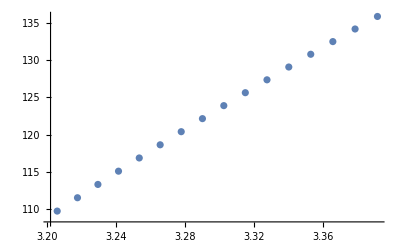

```mathematica
(*13 changes*)
energyIn=3*Sqrt[vals0p9[[1]]];
deltaWidth=.1;
pOut={};
total=500;
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals0p9[[i]]]-energyIn]<=deltaWidth,
AppendTo[pOut,i]];
];
Print[Length[pOut]];
mSquaredDecay={};
For[i=1,i<=Length[pOut],i++,
(*right*)
dkout[x_]:=(vecs0p9[[pOut[[i]]]]+I*vecs0p9[[pOut[[i]]-1]])/Sqrt[2];
mright=-I*Pi^2*κ*(1/3)*(4!)*2*Pi*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*vecs0p9[[1]]*vecs0p9[[1]]*vecs0p9[[1]]*dkout[x],{x,-L/2,L/2}];
(*left*)
dkout[x_]:=(vecs0p9[[pOut[[i]]]]-I*vecs0p9[[pOut[[i]]-1]])/Sqrt[2];
mleft=-I*Pi^2*κ*(1/3)*(4!)*2*Pi*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*vecs0p9[[1]]*vecs0p9[[1]]*vecs0p9[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[mSquaredDecay,Abs[mright]^2+Abs[mleft]^2];
];
ListPlot[Transpose[{Sqrt[vals0p9[[pOut]]],mSquaredDecay}]]
```

```mathematica
drate0p9=Mean[mSquaredDecay]
```

122.927

```mathematica
(*13 changes*)
(*g/kappa=1.1->3 level decay*)
g=1.1;
κ=1;
L=300;
dx=.01;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G1p1"]; 
PhiVSYKappa1G1p1=Interpolation[PhiVsYListKappa1G1p1,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G1p1[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-L/2,L/2,.01}];
ϕssint=Interpolation[data];
vals1p1=Import["/scratch/network/zz3250/valsL300dxp01g1p1.wl"];
vecs1p1=Import["/scratch/network/zz3250/vecsL300dxp01g1p1.wl"];
```

13

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0190486-0.0000150668 ⅈ and 0.000013764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0190486+0.0000150668 ⅈ and 0.000013764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0191155-0.0000152132 ⅈ and 0.0000138644 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

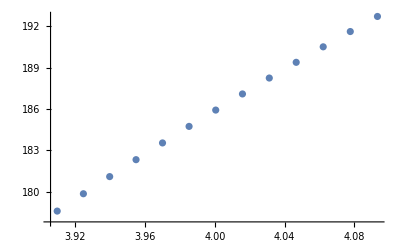

```mathematica
(*13 changes*)
energyIn=3*Sqrt[vals1p1[[1]]];
deltaWidth=.1;
pOut={};
total=500;
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals1p1[[i]]]-energyIn]<=deltaWidth,
AppendTo[pOut,i]];
];
Print[Length[pOut]];
mSquaredDecay={};
For[i=1,i<=Length[pOut],i++,
(*right*)
dkout[x_]:=(vecs1p1[[pOut[[i]]]]+I*vecs1p1[[pOut[[i]]-1]])/Sqrt[2];
mright=-I*Pi^2*κ*(1/3)*(4!)*2*Pi*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*vecs1p1[[1]]*vecs1p1[[1]]*vecs1p1[[1]]*dkout[x],{x,-L/2,L/2}];
(*left*)
dkout[x_]:=(vecs1p1[[pOut[[i]]]]-I*vecs1p1[[pOut[[i]]-1]])/Sqrt[2];
mleft=-I*Pi^2*κ*(1/3)*(4!)*2*Pi*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*vecs1p1[[1]]*vecs1p1[[1]]*vecs1p1[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[mSquaredDecay,Abs[mright]^2+Abs[mleft]^2];
];
ListPlot[Transpose[{Sqrt[vals1p1[[pOut]]],mSquaredDecay}]]
```

```mathematica
drate1p1=Mean[mSquaredDecay]
```

185.822

```mathematica
(*13 changes*)
(*g/kappa=1.3->2 level decay now possible!*)
g=1.3;
κ=1;
L=300;
dx=.01;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G1p3"]; 
PhiVSYKappa1G1p3=Interpolation[PhiVsYListKappa1G1p3,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G1p3[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-L/2,L/2,.01}];
ϕssint=Interpolation[data];
vals1p3=Import["/scratch/network/zz3250/valsL300dxp01g1p3.wl"];
vecs1p3=Import["/scratch/network/zz3250/vecsL300dxp01g1p3.wl"];
```

22

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000114875-0.0227744 ⅈ and 5.03767×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000114875+0.0227744 ⅈ and 5.03767×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000117093-0.0228835 ⅈ and 5.07969×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

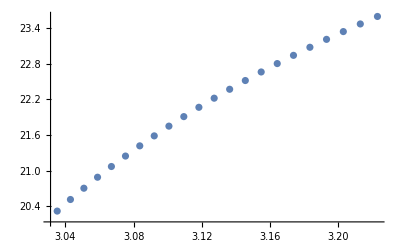

```mathematica
(*11 changes*)
energyIn=2*Sqrt[vals1p3[[1]]];
deltaWidth=.1;
pOut={};
total=500;
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals1p3[[i]]]-energyIn]<=deltaWidth,
AppendTo[pOut,i]];
];
Print[Length[pOut]];
mSquaredDecay={};
For[i=1,i<=Length[pOut],i++,
(*right*)
dkout[x_]:=(vecs1p3[[pOut[[i]]]]+I*vecs1p3[[pOut[[i]]-1]])/Sqrt[2];
mright=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p3[[1]]*vecs1p3[[1]]*dkout[x],{x,-L/2,L/2}];
(*left*)
dkout[x_]:=(vecs1p3[[pOut[[i]]]]-I*vecs1p3[[pOut[[i]]-1]])/Sqrt[2];
mleft=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p3[[1]]*vecs1p3[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[mSquaredDecay,Abs[mright]^2+Abs[mleft]^2];
];
ListPlot[Transpose[{Sqrt[vals1p3[[pOut]]],mSquaredDecay}]]
```

```mathematica
drate1p3=Mean[mSquaredDecay]
```

22.0749

```mathematica
(*13 changes*)
(*g/kappa=1.5->2 level decay*)
g=1.5;
κ=1;
L=300;
dx=.01;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G1p5"]; 
PhiVSYKappa1G1p5=Interpolation[PhiVsYListKappa1G1p5,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G1p5[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-L/2,L/2,.01}];
ϕssint=Interpolation[data];
vals1p5=Import["/scratch/network/zz3250/valsL300dxp01g1p5.wl"];
vecs1p5=Import["/scratch/network/zz3250/vecsL300dxp01g1p5.wl"];
```

17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000236898+0.0252345 ⅈ and 7.20359×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000236898-0.0252345 ⅈ and 7.20359×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000239606-0.0252912 ⅈ and 7.25824×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

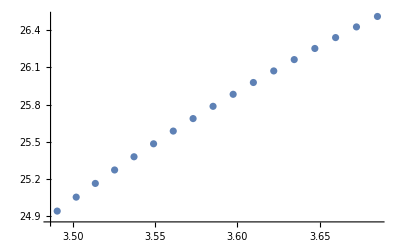

```mathematica
(*11 changes*)
energyIn=2*Sqrt[vals1p5[[1]]];
deltaWidth=.1;
pOut={};
total=500;
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals1p5[[i]]]-energyIn]<=deltaWidth,
AppendTo[pOut,i]];
];
Print[Length[pOut]];
mSquaredDecay={};
For[i=1,i<=Length[pOut],i++,
(*right*)
dkout[x_]:=(vecs1p5[[pOut[[i]]]]+I*vecs1p5[[pOut[[i]]-1]])/Sqrt[2];
mright=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p5[[1]]*vecs1p5[[1]]*dkout[x],{x,-L/2,L/2}];
(*left*)
dkout[x_]:=(vecs1p5[[pOut[[i]]]]-I*vecs1p5[[pOut[[i]]-1]])/Sqrt[2];
mleft=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p5[[1]]*vecs1p5[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[mSquaredDecay,Abs[mright]^2+Abs[mleft]^2];
];
ListPlot[Transpose[{Sqrt[vals1p5[[pOut]]],mSquaredDecay}]]
```

```mathematica
drate1p5=Mean[mSquaredDecay]
```

25.7633

```mathematica
(*13 changes*)
(*g/kappa=1.7->2 level decay*)
g=1.7;
κ=1;
L=300;
dx=.01;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G1p7"]; 
PhiVSYKappa1G1p7=Interpolation[PhiVsYListKappa1G1p7,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G1p7[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-L/2,L/2,.01}];
ϕssint=Interpolation[data];
vals1p7=Import["/scratch/network/zz3250/valsL300dxp01g1p7.wl"];
vecs1p7=Import["/scratch/network/zz3250/vecsL300dxp01g1p7.wl"];
```

15

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000358622+0.026303 ⅈ and 9.86532×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000358622-0.026303 ⅈ and 9.86532×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.00003617+0.0263386 ⅈ and 9.93789×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

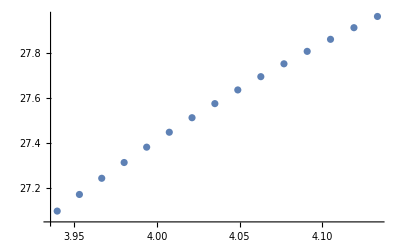

```mathematica
(*11 changes*)
energyIn=2*Sqrt[vals1p7[[1]]];
deltaWidth=.1;
pOut={};
total=500;
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals1p7[[i]]]-energyIn]<=deltaWidth,
AppendTo[pOut,i]];
];
Print[Length[pOut]];
mSquaredDecay={};
For[i=1,i<=Length[pOut],i++,
(*right*)
dkout[x_]:=(vecs1p7[[pOut[[i]]]]+I*vecs1p7[[pOut[[i]]-1]])/Sqrt[2];
mright=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p7[[1]]*vecs1p7[[1]]*dkout[x],{x,-L/2,L/2}];
(*left*)
dkout[x_]:=(vecs1p7[[pOut[[i]]]]-I*vecs1p7[[pOut[[i]]-1]])/Sqrt[2];
mleft=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p7[[1]]*vecs1p7[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[mSquaredDecay,Abs[mright]^2+Abs[mleft]^2];
];
ListPlot[Transpose[{Sqrt[vals1p7[[pOut]]],mSquaredDecay}]]
```

```mathematica
drate1p7=Mean[mSquaredDecay]
```

27.5579

```mathematica
(*13 changes*)
(*g/kappa=1.9->2 level decay*)
g=1.9;
κ=1;
L=300;
dx=.01;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G1p9"]; 
PhiVSYKappa1G1p9=Interpolation[PhiVsYListKappa1G1p9,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G1p9[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-L/2,L/2,.01}];
ϕssint=Interpolation[data];
vals1p9=Import["/scratch/network/zz3250/valsL300dxp01g1p9.wl"];
vecs1p9=Import["/scratch/network/zz3250/vecsL300dxp01g1p9.wl"];
```

13

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000603154+0.0267683 ⅈ and 0.0000134838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000603154-0.0267683 ⅈ and 0.0000134838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000607498+0.0267872 ⅈ and 0.0000135773 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

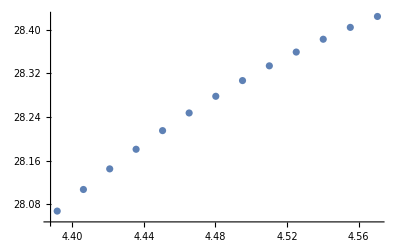

```mathematica
(*11 changes*)
energyIn=2*Sqrt[vals1p9[[1]]];
deltaWidth=.1;
pOut={};
total=500;
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals1p9[[i]]]-energyIn]<=deltaWidth,
AppendTo[pOut,i]]
];
Print[Length[pOut]];
mSquaredDecay={};
For[i=1,i<=Length[pOut],i++,
(*right*)
dkout[x_]:=(vecs1p9[[pOut[[i]]]]+I*vecs1p9[[pOut[[i]]-1]])/Sqrt[2];
mright=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p9[[1]]*vecs1p9[[1]]*dkout[x],{x,-L/2,L/2}];
(*left*)
dkout[x_]:=(vecs1p9[[pOut[[i]]]]-I*vecs1p9[[pOut[[i]]-1]])/Sqrt[2];
mleft=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p9[[1]]*vecs1p9[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[mSquaredDecay,Abs[mright]^2+Abs[mleft]^2];
];
ListPlot[Transpose[{Sqrt[vals1p9[[pOut]]],mSquaredDecay}]]
```

```mathematica
drate1p9=Mean[mSquaredDecay]
```

28.2653

```mathematica
(*13 changes*)
(*g/kappa=2.1->2 level decay*)
g=2.1;
κ=1;
L=300;
dx=.01;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa1G2p1"]; 
PhiVSYKappa1G2p1=Interpolation[PhiVsYListKappa1G2p1,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G2p1[(Pi^(1/2)*Exp[(2*Pi*κ)^(1/2)x])/(1+Exp[(2*Pi*κ)^(1/2)x])];
data=Table[{x,ϕss[x]},{x,-L/2,L/2,.01}];
ϕssint=Interpolation[data];
vals2p1=Import["/scratch/network/zz3250/valsL300dxp01g2p1.wl"];
vecs2p1=Import["/scratch/network/zz3250/vecsL300dxp01g2p1.wl"];
```

13

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000722167+0.0268467 ⅈ and 0.0000175838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000722167-0.0268467 ⅈ and 0.0000175838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000726419+0.0268518 ⅈ and 0.0000176985 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

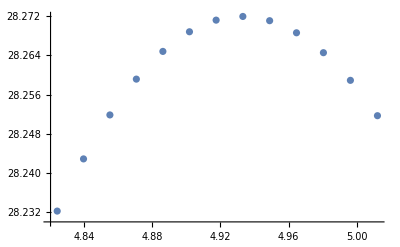

```mathematica
(*11 changes*)
energyIn=2*Sqrt[vals2p1[[1]]];
deltaWidth=.1;
pOut={};
total=500;
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals2p1[[i]]]-energyIn]<=deltaWidth,
AppendTo[pOut,i]]
];
Print[Length[pOut]];
mSquaredDecay={};
For[i=1,i<=Length[pOut],i++,
(*right*)
dkout[x_]:=(vecs2p1[[pOut[[i]]]]+I*vecs2p1[[pOut[[i]]-1]])/Sqrt[2];
mright=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs2p1[[1]]*vecs2p1[[1]]*dkout[x],{x,-L/2,L/2}];
(*left*)
dkout[x_]:=(vecs2p1[[pOut[[i]]]]-I*vecs2p1[[pOut[[i]]-1]])/Sqrt[2];
mleft=-I*(2/3)*Pi^(3/2)*κ*(3!)*2*Pi*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs2p1[[1]]*vecs2p1[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[mSquaredDecay,Abs[mright]^2+Abs[mleft]^2];
];
ListPlot[Transpose[{Sqrt[vals2p1[[pOut]]],mSquaredDecay}]]
```

```mathematica
drate2p1=Mean[mSquaredDecay]
```

28.2598

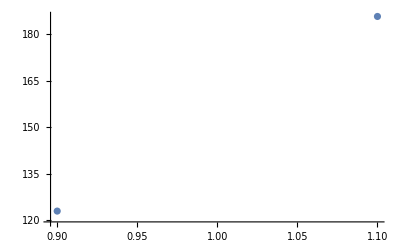

```mathematica
threelevel={drate0p9,drate1p1};
gkap={.9,1.1};
ListPlot[Transpose[{gkap,threelevel}]]
```

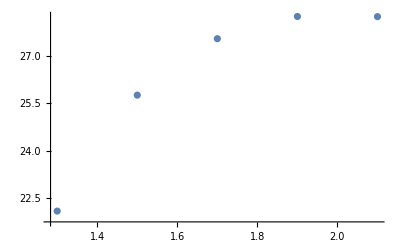

```mathematica
twolevel={drate1p3,drate1p5,drate1p7,drate1p9,drate2p1};
gkap={1.3,1.5,1.7,1.9,2.1};
ListPlot[Transpose[{gkap,twolevel}]]
```

```mathematica
(*Time dependent decay probability*)
coeff=4*Pi^3*κ^2/(9*L*vals1p5[[1]]);
decayrateexpr=0;
For[i=3,i<=total,i=i+2,
Vbbp=NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p5[[1]]*vecs1p5[[1]]*(vecs1p5[[i]]+I*vecs1p5[[i-1]])/Sqrt[2],{x,-L/2,L/2}];
decay=coeff*(Abs[Vbbp]^2/Sqrt[vals1p5[[i]]])*Sin[(Sqrt[vals1p5[[i]]]/2-Sqrt[vals1p5[[1]]])*t]^2/(2*Sqrt[vals1p5[[1]]]-Sqrt[vals1p5[[i]]])^2;
decayrateexpr=decayrateexpr+decay;
];
decayrate[t_]:=decayrateexpr;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -2.49739×10^-7-0.000732276 ⅈ and 1.5148×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -4.99453×10^-7+0.00146277 ⅈ and 3.02644×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 7.4917×10^-7-0.00218971 ⅈ and 4.53181×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

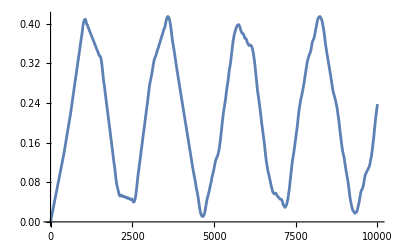

```mathematica
Plot[decayrate[t],{t,0,10000}]
```

```mathematica
(*Time dependent decay rate*)
coeff=4*Pi^3*κ^2/(9*L*vals1p5[[1]]);
decayrateexpr=0;
For[i=3,i<=total,i=i+2,
Vbbp=NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*vecs1p5[[1]]*vecs1p5[[1]]*(vecs1p5[[i]]+I*vecs1p5[[i-1]])/Sqrt[2],{x,-L/2,L/2}];
decay=coeff*(Abs[Vbbp]^2/Sqrt[vals1p5[[i]]])*Sin[(Sqrt[vals1p5[[i]]]-2*Sqrt[vals1p5[[1]]])*t]/(2*Sqrt[vals1p5[[1]]]-Sqrt[vals1p5[[i]]]);
decayrateexpr=decayrateexpr+decay;
];
rateofdecay[t_]:=decayrateexpr;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -2.49739×10^-7-0.000732276 ⅈ and 1.5148×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -4.99453×10^-7+0.00146277 ⅈ and 3.02644×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 7.4917×10^-7-0.00218971 ⅈ and 4.53181×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

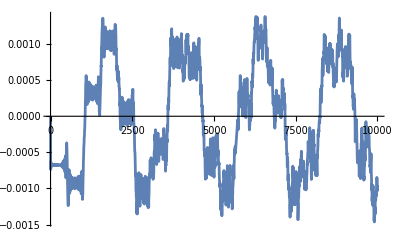

```mathematica
Plot[rateofdecay[t],{t,0,10000}]
```